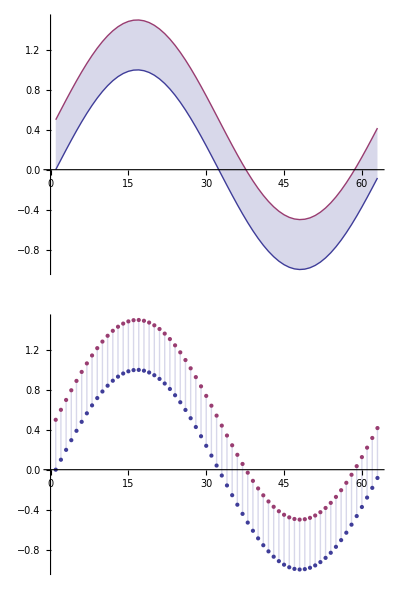

```mathematica
x=Range[0,2π,0.1];
y={Sin[x],Sin[x]+0.5};
ListPlot[y,Filling->{1->{2}},Joined->#]&/@{True,False};
%//Column
```

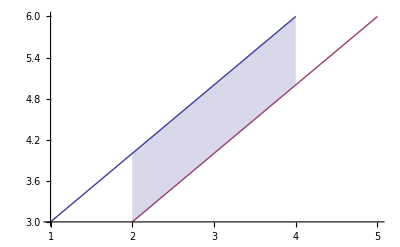

```mathematica
d1=Import["./mathematica/data.txt","Table"];
d2=d1[[;;,#]]&/@{{1,3},{2,3}};
ListLinePlot[d2,Filling->{1->{2}},Frame->1]
```

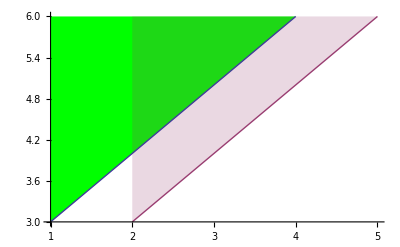

```mathematica
ListLinePlot[d2,Frame->1,Filling->{2->Top,1->{Top,Green}}]
```

## debug area

```mathematica
data=Table[{{x,Sin[x]},{x,Cos[x]}},{x,0,2π,0.1}];
plt=ListLinePlot[Transpose@data,Filling->{1->{2}}];
poly=Cases[Normal@plt,Polygon[p_]:>p,-1];

RegionPlot[Graphics`Mesh`InPolygonQ[#,{x,y}]&/@poly//Evaluate,{x,0,2π},{y,-1.5,1.5},Mesh->50,PlotPoints->50,MeshFunctions->{#-#2&},MeshShading->{None},BoundaryStyle->Black]//Quiet
```

-Graphics-